```mathematica
csss[x1_,y1_,z1_,r1_,x2_,y2_,z2_,r2_,x3_,y3_,z3_,r3_,an_]:=Module[{m,n,A,B,C,D,E,F,a,x,y,z,r,xyzs,zs},
m={{-2 x1+2 x2,-2 y1+2 y2,-2 z1+2 z2,-2 r1+2 r2,-x1^2+x2^2-y1^2+y2^2-z1^2+z2^2+r1^2-r2^2},{-2 x2+2 x3,-2 y2+2 y3,-2 z2+2 z3,-2 r2+2 r3,-x2^2+x3^2-y2^2+y3^2-z2^2+z3^2+r2^2-r3^2}};n=RowReduce[m];A=n⟦1,5⟧;B=n⟦1,4⟧;C=n⟦1,3⟧;D=n⟦2,5⟧;E=n⟦2,4⟧;F=n⟦2,3⟧;
a=an ;
r=Min[r/.{ToRules[Reduce[((1/(2 (C^2 Cos[a]^2+F^2 Cos[a]^2-Sin[a]^2))(2 A C Cos[a]^2+2 D F Cos[a]^2-2 B C r Cos[a]^2-2 ⅇ F r Cos[a]^2-2 r Sin[a])-1/(2 (1+C^2+F^2))(2 A C+2 D F-2 B C r-2 ⅇ F r-2 C x1-2 F y1+2 z1))^2-1/(4(1+C^2+F^2)^2)((-2 A C-2 D F+2 B C r+2 ⅇ F r+2 C x1+2 F y1-2 z1)^2-4 (1+C^2+F^2) (A^2+D^2-2 A B r-2 D ⅇ r-r^2+B^2 r^2+ⅇ^2 r^2-2 r r1-r1^2-2 A x1+2 B r x1+x1^2-2 D y1+2 ⅇ r y1+y1^2+z1^2))-1/(4(C^2 Cos[a]^2+F^2 Cos[a]^2-Sin[a]^2)^2)((-2 A C Cos[a]^2-2 D F Cos[a]^2+2 B C r Cos[a]^2+2 ⅇ F r Cos[a]^2+2 r Sin[a])^2-4 (-r^2+A^2 Cos[a]^2+D^2 Cos[a]^2-2 A B r Cos[a]^2-2 D ⅇ r Cos[a]^2+B^2 r^2 Cos[a]^2+ⅇ^2 r^2 Cos[a]^2) (C^2 Cos[a]^2+F^2 Cos[a]^2-Sin[a]^2)))^2-4*1/(4(1+C^2+F^2)^2)((-2 A C-2 D F+2 B C r+2 ⅇ F r+2 C x1+2 F y1-2 z1)^2-4 (1+C^2+F^2) (A^2+D^2-2 A B r-2 D ⅇ r-r^2+B^2 r^2+ⅇ^2 r^2-2 r r1-r1^2-2 A x1+2 B r x1+x1^2-2 D y1+2 ⅇ r y1+y1^2+z1^2))*1/(4(C^2 Cos[a]^2+F^2 Cos[a]^2-Sin[a]^2)^2)((-2 A C Cos[a]^2-2 D F Cos[a]^2+2 B C r Cos[a]^2+2 ⅇ F r Cos[a]^2+2 r Sin[a])^2-4 (-r^2+A^2 Cos[a]^2+D^2 Cos[a]^2-2 A B r Cos[a]^2-2 D ⅇ r Cos[a]^2+B^2 r^2 Cos[a]^2+ⅇ^2 r^2 Cos[a]^2) (C^2 Cos[a]^2+F^2 Cos[a]^2-Sin[a]^2))==0,r,Reals, Quartics->True]]}];
Return[r]
]
```

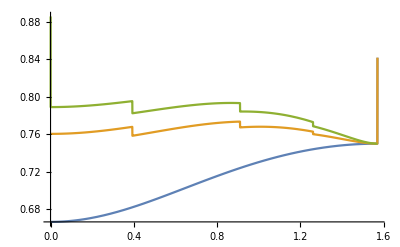

```mathematica
Plot[{((Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ])))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ])))/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4))),
(Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ]))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ]))+4/3*Pi*((Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2)^3*Floor[2 Pi/(2*ArcSin[1/(2+Cos[θ])])])/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4))),
(Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ]))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ]))+4/3*Pi*((Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2)^3*Floor[2 Pi/(2*ArcSin[1/(2+Cos[θ])])]+(4/3*Pi*csss[0,0,Csc[θ],1,((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[0],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[0],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[2*ArcSin[1/(2+Cos[θ])]],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[2*ArcSin[1/(2+Cos[θ])]],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,θ]^3+4/3*Pi*csss[0,0,Csc[θ]+1+(Sec[θ]+Tan[θ])^2,(Sec[θ]+Tan[θ])^2,((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[0],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[0],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[2*ArcSin[1/(2+Cos[θ])]],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[2*ArcSin[1/(2+Cos[θ])]],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,θ]^3)*(Floor[2 Pi/(2*ArcSin[1/(2+Cos[θ])])]-1))/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4)))},{θ,0,Pi/2}]
```